Linear stability analysis of the homogeneous steady state [gray regions in Fig. 11(a,b)];

```mathematica
f=u^2 v-u;
source=p-u;
fTot={f,source,0};(*change depending on source being in u or v*)
```

```mathematica
fixedParams={Du->1,p->2,L->20}
```

{Du→1,p→2,L→20}

### Fixed point (homogenous steady state, hss)

```mathematica
fp=First@Solve[Thread[{f,-f}+eps fTot[[2;;]]==0]/.{n->(u+v),eta->(v+Du/Dv u)},{u,v}]
```

{u→p,v→1/p}

### Linear stability

```mathematica
jac=(DiagonalMatrix[{-Du q2,-Dv q2}]+D[({f,-f}+eps fTot[[2;;]])/.{n->(u+v),eta->(v+Du/Dv u)},{{u,v}}])/.fp;
jac//MatrixForm
```

(1-eps-Du q2 | p^2
-1 | -p^2-Dv q2)

```mathematica
Eigenvalues[jac]/.q2->0
```

{1/2 (1-eps-p^2-√(-4 eps p^2+(-1+eps+p^2)^2)),1/2 (1-eps-p^2+√(-4 eps p^2+(-1+eps+p^2)^2))}

For p>1, the hss is stable against homogeneous perturbations.
Find the edges of the band of unstable modes:

```mathematica
unstableBand=q2/.Solve[Eigenvalues[jac][[2]]==0,q2];
```

### Stability threshold on infinite domain

Find onset where unstable band emerges;
assure that the band lies at positive q^2

```mathematica
epsC=Assuming[{unstableBand[[1]]>0,unstableBand[[2]]>0,eps>0},eps/.First@Solve[Evaluate[unstableBand[[1]]==unstableBand[[2]]],eps]]
```

ConditionalExpression[-2 √((Du p^2)/Dv)+(Dv+Du p^2)/Dv, ]

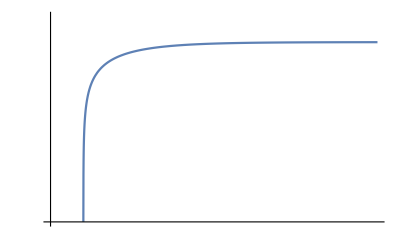

```mathematica
LogLogPlot[Evaluate[epsC/.fixedParams],{Dv,1,10^6},
PlotRange->{10^-7,10},
Ticks->{{{1,},{10^6,}},{{10^-7,},{10^0,}}}]
```